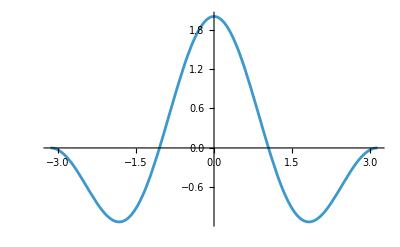

```mathematica
Plot[Cos[k]+Cos[2*k],{k,-Pi,Pi}]
```

```mathematica
Minimize[Cos[k]+Cos[2*k],k]
```

{Cos[2 ArcTan[√(5/3)]]+Cos[4 ArcTan[√(5/3)]],{k→-2 (24 π+ArcTan[√(5/3)])}}

```mathematica
N[2*ArcTan[Sqrt[5/3]]]
N[ArcCos[-1/4]]
```

1.82348

1.82348

## Single triangular plaquette

### Two spin ups

The basis is ↑↑0, ↑0↑, 0↑↑.

```mathematica
HTriPlqt2up=-{{0,1,1},{1,0,1},{1,1,0}};
TraditionalForm[HTriPlqt2up]
Eigensystem[HTriPlqt2up]
```

(0 | -1 | -1
-1 | 0 | -1
-1 | -1 | 0)

{{-2,1,1},{{1,1,1},{-1,0,1},{-1,1,0}}}

### One spin up, one spin down

The basis is ↑↓0, ↑0↓, ↓↑0, ↓0↑, 0↑↓, 0↓↑.

```mathematica
HTriPlqt1up1dn=-{{0,1,0,0,0,1},{1,0,0,0,1,0},{0,0,0,1,1,0},{0,0,1,0,0,1},{0,1,1,0,0,0},{1,0,0,1,0,0}};
TraditionalForm[HTriPlqt1up1dn]
Eigensystem[HTriPlqt1up1dn]
```

(0 | -1 | 0 | 0 | 0 | -1
-1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | -1 | 0
0 | 0 | -1 | 0 | 0 | -1
0 | -1 | -1 | 0 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0)

{{-2,2,-1,-1,1,1},{{1,1,1,1,1,1},{-1,1,1,-1,-1,1},{1,0,-1,0,-1,1},{-1,-1,1,1,0,0},{-1,0,-1,0,1,1},{-1,1,-1,1,0,0}}}

## Two sites

```mathematica
Eigensystem[{{-Q, t},{t, Q}}]
```

{{-√(Q^2+t^2),√(Q^2+t^2)},{{-(Q+√(Q^2+t^2))/t,1},{-(Q-√(Q^2+t^2))/t,1}}}